```mathematica
(**** This notebook contains the analysis and visualization of the experiments with the 3 data-generation scenarios ****)

(* Wilson confidence interval (CI) for the Binomial distribution parameter. 
   - jj: count of successes
- nn: count of attempts
- confLvl: confidence level for the CI *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]];
```

```mathematica
(*** STATIC SCENARIO ANALYSIS ***)
```

```mathematica
(* loading the files *) 
statDataPPnaive= Import[NotebookDirectory[]<>"generated_data/static/static_baseline_naive.csv"];
statDataPPaccurate = Import[NotebookDirectory[]<>"generated_data/static/static_baseline_accurate.csv"];
statDataOurs= Import[NotebookDirectory[]<>"generated_data/static/static_ours.csv"];
```

```mathematica
statLen = Length@statDataPPaccurate; If[Length@statDataPPaccurate ≠ Length@statDataPPnaive ∨ Length@statDataPPaccurate ≠ Length@statDataOurs, Throw["Data length different"]];
```

```mathematica
(* making sequential sublists of the data, length from 1 to all *) 
statDataPPnaiveSlices = Table[statDataPPnaive[[1;;i]], {i, 1, statLen}] ;statDataPPaccurateSlices = Table[statDataPPaccurate[[1;;i]], {i, 1, statLen}] ;
statDataOursSlices =  Table[statDataOurs[[1;;i]], {i, 1, statLen}] ;
```

```mathematica
(* Test 1: marginal prob of first variable being day *)
```

```mathematica
interWilson[Count[statDataPPnaive[[All,1]], "day"],statLen, 0.95]
interWilson[Count[statDataPPaccurate[[All,1]], "day"],statLen, 0.95]
interWilson[Count[statDataOurs[[All,1]], "day"],statLen, 0.95]
```

Interval[{0.588455,0.60767}]

Interval[{0.58103,0.600301}]

Interval[{0.590261,0.609462}]

```mathematica
dayIntsPPnaive = interWilson[Count[#[[All,1]], "day"],Length@#, 0.95]&/@ statDataPPnaiveSlices;
dayIntsPPaccurate = interWilson[Count[#[[All,1]], "day"],Length@#, 0.95]&/@ statDataPPaccurateSlices;
dayIntsPPours = interWilson[Count[#[[All,1]], "day"],Length@#, 0.95]&/@ statDataOursSlices;
```

Part::pkspec1: The expression Floor[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

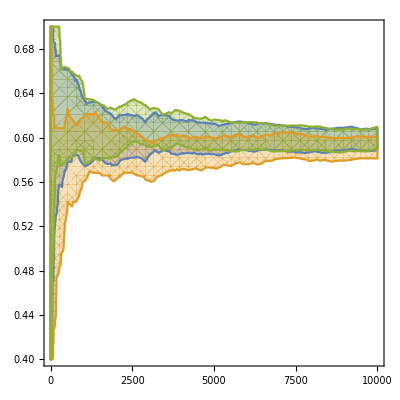

```mathematica
RegionPlot[{IntervalMemberQ[dayIntsPPnaive[[ Floor@x ]], y], IntervalMemberQ[dayIntsPPaccurate[[ Floor@x ]], y], IntervalMemberQ[dayIntsPPours[[ Floor@x ]],y]},{x,1,statLen},{y,0.4,0.7}]
```

```mathematica
(* Test 2: marginal prob of second variable being detected *)
```

```mathematica
interWilson[Count[statDataPPnaive[[All,2]], "detected"],statLen, 0.95]
interWilson[Count[statDataPPaccurate[[All,2]], "detected"],statLen, 0.95]
interWilson[Count[statDataOurs[[All,2]], "detected"],statLen, 0.95]
```

Interval[{0.557565,0.576983}]

Interval[{0.549949,0.569405}]

Interval[{0.56388,0.583263}]

```mathematica
detIntsPPnaive = interWilson[Count[#[[All,2]], "detected"],Length@#, 0.95]&/@ statDataPPnaiveSlices;
detIntsPPaccurate = interWilson[Count[#[[All,2]], "detected"],Length@#, 0.95]&/@ statDataPPaccurateSlices;
detIntsPPours = interWilson[Count[#[[All,2]], "detected"],Length@#, 0.95]&/@ statDataOursSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

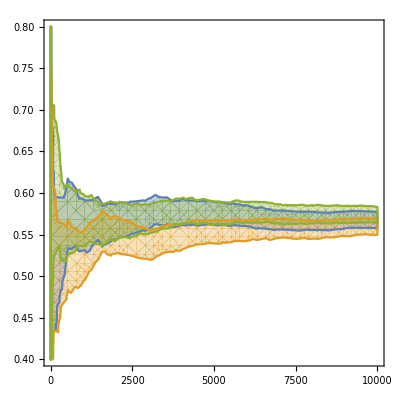

```mathematica
RegionPlot[{IntervalMemberQ[detIntsPPnaive[[ Ceiling@x ]], y], IntervalMemberQ[detIntsPPaccurate[[ Ceiling@x ]], y], IntervalMemberQ[detIntsPPours[[ Ceiling@x ]], y]},{x,1,statLen},{y,0.4,0.8}]
```

```mathematica
(* Test 3: marginal prob of third variable being in; observing the bias here *)
```

```mathematica
interWilson[Count[statDataPPnaive[[All,3]], "in"],statLen, 0.95]
interWilson[Count[statDataPPaccurate[[All,3]], "in"],statLen, 0.95]
interWilson[Count[statDataOurs[[All,3]], "in"],statLen, 0.95]
```

Interval[{0.787989,0.803784}]

Interval[{0.789003,0.804769}]

Interval[{0.790727,0.806444}]

```mathematica
inIntsPPnaive = interWilson[Count[#[[All,3]], "in"],Length@#, 0.95]&/@ statDataPPnaiveSlices;
inIntsPPaccurate = interWilson[Count[#[[All,3]], "in"],Length@#, 0.95]&/@ statDataPPaccurateSlices;
inIntsOurs = interWilson[Count[#[[All,3]], "in"],Length@#, 0.95]&/@ statDataOursSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

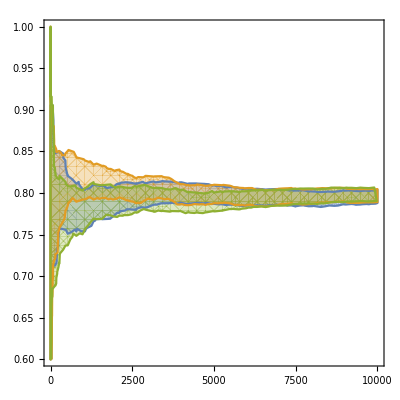

```mathematica
RegionPlot[{IntervalMemberQ[inIntsPPnaive[[ Ceiling@x ]], y], IntervalMemberQ[inIntsPPaccurate[[ Ceiling@x ]], y], IntervalMemberQ[inIntsOurs[[ Ceiling@x ]], y]},{x,1,statLen},{y,0.6,1}]
```

```mathematica
(* Test 4: joint prob of all good *)
```

```mathematica
interWilson[Count[statDataPPnaive, {"day", "detected", "in"}],statLen, 0.95]
interWilson[Count[statDataPPaccurate, {"day", "detected", "in"}],statLen, 0.95]
interWilson[Count[statDataOurs, {"day", "detected", "in"}],statLen, 0.95]
```

Interval[{0.347467,0.366243}]

Interval[{0.356314,0.37519}]

Interval[{0.373917,0.392973}]

```mathematica
allGoodIntsPPnaive = interWilson[Count[#, {"day", "detected", "in"}],Length@#, 0.95]&/@ statDataPPnaiveSlices;
allGoodIntsPPaccurate = interWilson[Count[#, {"day", "detected", "in"}],Length@#, 0.95]&/@ statDataPPaccurateSlices;
allGoodIntsOurs = interWilson[Count[#, {"day", "detected", "in"}],Length@#, 0.95]&/@ statDataOursSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

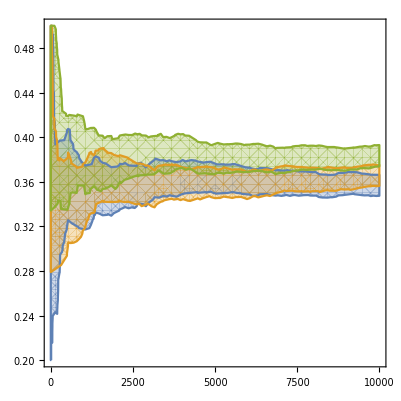

```mathematica
RegionPlot[{IntervalMemberQ[allGoodIntsPPnaive[[ Ceiling@x ]], y], IntervalMemberQ[allGoodIntsPPaccurate[[ Ceiling@x ]], y],IntervalMemberQ[allGoodIntsOurs[[ Ceiling@x ]], y]},{x,1,statLen},{y,0.2,0.5}]
```

```mathematica
(* joint prob of all bad - probabilities too small *)
```

```mathematica
interWilson[Count[statDataPPnaive, {"night", "not detected", "out"}],statLen, 0.95]
interWilson[Count[statDataPPaccurate, {"night", "not detected", "out"}],statLen, 0.95]
interWilson[Count[statDataOurs, {"night", "not detected", "out"}],statLen, 0.95]
```

Interval[{0.021924,0.0436655}]

Interval[{0.0312209,0.0562844}]

Interval[{0.0337995,0.0596828}]

```mathematica
(* joint prob of "in" and "detected", also bias noticed *)
```

```mathematica
interWilson[Count[statDataPPnaive,{_, "detected", "in"}],statLen, 0.95]
interWilson[Count[statDataPPaccurate, {_, "detected", "in"}],statLen, 0.95]
interWilson[Count[statDataOurs, {_, "detected", "in"}],statLen, 0.95]
```

Interval[{0.44496,0.464475}]

Interval[{0.461629,0.481193}]

Interval[{0.475812,0.495399}]

```mathematica
(* joint prob of "in" and "not detected", also bias noticed *)
```

```mathematica
interWilson[Count[statDataPPnaive,{_, "not detected", "in"}],statLen, 0.95]
interWilson[Count[statDataPPaccurate, {_, "not detected", "in"}],statLen, 0.95]
interWilson[Count[statDataOurs, {_, "not detected", "in"}],statLen, 0.95]
```

Interval[{0.332069,0.350652}]

Interval[{0.316484,0.33485}]

Interval[{0.304084,0.32226}]

```mathematica
(* joint prob of "out" and "detected", also bias noticed *)
```

```mathematica
interWilson[Count[statDataPPnaive,{_, "detected", "out"}],statLen, 0.95]
interWilson[Count[statDataPPaccurate, {_, "detected", "out"}],statLen, 0.95]
interWilson[Count[statDataOurs, {_, "detected", "out"}],statLen, 0.95]
```

Interval[{0.106553,0.118945}]

Interval[{0.0828959,0.0940203}]

Interval[{0.0826045,0.0937119}]

```mathematica
outDetIntsPPnaive = interWilson[Count[#, {_, "detected", "out"}],Length@#, 0.95]&/@ statDataPPnaiveSlices;
outDetIntsPPaccurate = interWilson[Count[#, {_, "detected", "out"}],Length@#, 0.95]&/@ statDataPPaccurateSlices;
outDetIntsOurs = interWilson[Count[#, {_, "detected", "out"}],Length@#, 0.95]&/@ statDataOursSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

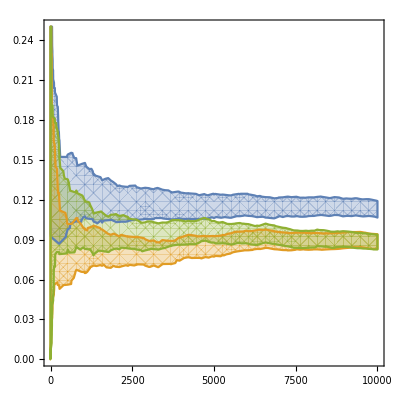

```mathematica
RegionPlot[{IntervalMemberQ[outDetIntsPPnaive[[ Ceiling@x ]], y], IntervalMemberQ[outDetIntsPPaccurate[[ Ceiling@x ]], y],IntervalMemberQ[outDetIntsOurs[[ Ceiling@x ]], y]},{x,1,statLen},{y,0,0.25}]
```

```mathematica
(* cond prob "detected" |  "out" , very biased *)
```

```mathematica
interWilson[Count[statDataPPnaive,{_, "detected", "out"}],Count[statDataPPnaive,{_,_, "out"}], 0.95]
interWilson[Count[statDataPPaccurate, {_, "detected", "out"}],Count[statDataPPnaive,{_,_, "out"}], 0.95]
interWilson[Count[statDataOurs, {_, "detected", "out"}],Count[statDataPPnaive,{_,_, "out"}], 0.95]
```

Interval[{0.530304,0.573423}]

Interval[{0.411489,0.45445}]

Interval[{0.41003,0.452974}]

```mathematica
detOutIntsPPnaive = interWilson[Count[#, {_, "detected", "out"}],Count[#,{_,_, "out"}], 0.95]&/@ statDataPPnaiveSlices[[100;;All]];
detOutIntsPPaccurate = interWilson[Count[#, {_, "detected", "out"}],Count[#,{_,_, "out"}], 0.95]&/@ statDataPPaccurateSlices[[100;;All]];
detOutIntsOurs = interWilson[Count[#, {_, "detected", "out"}],Count[#,{_,_, "out"}], 0.95]&/@ statDataOursSlices[[100;;All]];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

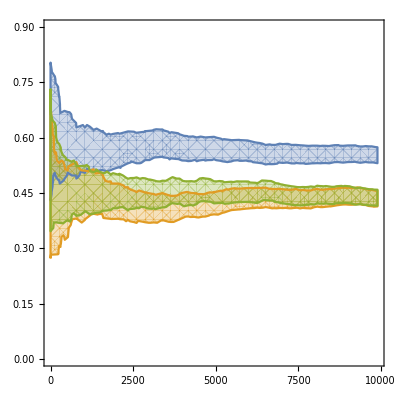

```mathematica
RegionPlot[{IntervalMemberQ[detOutIntsPPnaive[[ Ceiling@x ]], y], IntervalMemberQ[detOutIntsPPaccurate[[ Ceiling@x ]], y],IntervalMemberQ[detOutIntsOurs[[ Ceiling@x ]], y]},{x,1,statLen-100},{y,0,0.9}]
```

```mathematica
(*** INVARIANT EXAMPLE ANALYSIS ***)
```

```mathematica
(* loading the files *) 
invDataPPnaive= Import[NotebookDirectory[]<>"generated_data/time_invariant/time_invariant_baseline_naive.csv"];
invDataPPaccurate = Import[NotebookDirectory[]<>"generated_data/time_invariant/time_invariant_baseline_accurate.csv"];
invDataOurs= Import[NotebookDirectory[]<>"generated_data/time_invariant/time_invariant_ours.csv"];
```

```mathematica
invLen = Length@invDataPPaccurate; If[Length@invDataPPaccurate ≠ Length@invDataPPnaive ∨ Length@invDataPPaccurate ≠ Length@invDataOurs, Throw["Data length different"]];
```

```mathematica
(* making sequential sublists of the data, length from 1 to all *) 
invDataPPnaiveSlices = Table[invDataPPnaive[[1;;i]], {i, 1, invLen}] ;invDataPPaccurateSlices = Table[invDataPPaccurate[[1;;i]], {i, 1, invLen}] ;
invDataOursSlices =  Table[invDataOurs[[1;;i]], {i, 1, invLen}] ;
```

```mathematica
(* Test 1 - the first variable is high *) 
interWilson[Count[invDataPPnaive[[All,1]], "high"],invLen, 0.95]
interWilson[Count[invDataPPaccurate[[All,1]], "high"],invLen, 0.95]
interWilson[Count[invDataOurs[[All,1]], "high"],invLen, 0.95]
```

Interval[{0.191685,0.207346}]

Interval[{0.186959,0.202476}]

Interval[{0.189814,0.205418}]

```mathematica
(* Test 2 - the second variable is low *) 
interWilson[Count[invDataPPnaive[[All,2]], "low"],invLen, 0.95]
interWilson[Count[invDataPPaccurate[[All,2]], "low"],invLen, 0.95]
interWilson[Count[invDataOurs[[All,2]], "low"],invLen, 0.95]
```

Interval[{0.457735,0.47729}]

Interval[{0.460231,0.479792}]

Interval[{0.450947,0.470483}]

```mathematica
(* Test 3 - joint prob of both low *) 
interWilson[Count[invDataPPnaive, {"low", "low"}],invLen, 0.95]
interWilson[Count[invDataPPaccurate, {"low", "low"}],invLen, 0.95]
interWilson[Count[invDataOurs, {"low", "low"}],invLen, 0.95]
```

Interval[{0.374613,0.393676}]

Interval[{0.381878,0.401006}]

Interval[{0.37332,0.39237}]

```mathematica
(* Test 4 - joint prob of low + high *) 
interWilson[Count[invDataPPnaive, {"low", "high"}],invLen, 0.95]
interWilson[Count[invDataPPaccurate, {"low", "high"}],invLen, 0.95]
interWilson[Count[invDataOurs, {"low", "high"}],invLen, 0.95]
```

Interval[{0.406872,0.426192}]

Interval[{0.404381,0.423685}]

Interval[{0.41006,0.429402}]

```mathematica
(* Test 5 - joint prob of high + low *)
```

```mathematica
interWilson[Count[invDataPPnaive, {"high", "low"}],invLen, 0.95]
interWilson[Count[invDataPPaccurate, {"high", "low"}],invLen, 0.95]
interWilson[Count[invDataOurs, {"high", "low"}],invLen, 0.95]
```

Interval[{0.0781396,0.0889803}]

Interval[{0.0734858,0.0840378}]

Interval[{0.0728076,0.0833166}]

```mathematica
(* Test 6 - joint prob of both hight *)
```

```mathematica
interWilson[Count[invDataPPnaive, {"high", "high"}],invLen, 0.95]
interWilson[Count[invDataPPaccurate, {"high", "high"}],invLen, 0.95]
interWilson[Count[invDataOurs, {"high", "high"}],invLen, 0.95]
```

Interval[{0.109871,0.122424}]

Interval[{0.109871,0.122424}]

Interval[{0.113386,0.126106}]

```mathematica
(* Test 7 - going across time steps now: the first variable stays the same *)
```

```mathematica
interWilson[Count[(Partition[invDataPPnaive, 2,1]), _?(#[[1,1]] == #[[2,1]] &)],invLen-1, 0.95]
interWilson[Count[(Partition[invDataPPaccurate, 2,1]), _?(#[[1,1]] == #[[2,1]] &)],invLen-1, 0.95]
interWilson[Count[(Partition[invDataOurs, 2,1]), _?(#[[1,1]] == #[[2,1]] &)],invLen-1, 0.95]
```

Interval[{0.669246,0.687553}]

Interval[{0.675895,0.6941}]

Interval[{0.673577,0.691819}]

```mathematica
(* Test 8 - going across time steps now: the second variable (ping) stays the same, big bias here *)
```

```mathematica
interWilson[Count[(Partition[invDataPPnaive, 2,1]), _?(#[[1,2]] == #[[2,2]] &)],invLen-1, 0.95]
interWilson[Count[(Partition[invDataPPaccurate, 2,1]), _?(#[[1,2]] == #[[2,2]] &)],invLen-1, 0.95]
interWilson[Count[(Partition[invDataOurs, 2,1]), _?(#[[1,2]] == #[[2,2]] &)],invLen-1, 0.95]
```

Interval[{0.492051,0.511648}]

Interval[{0.669548,0.68785}]

Interval[{0.663808,0.682194}]

```mathematica
(* these take a bit of time *) 
pingFlipIntsPPnaive = interWilson[Count[(Partition[#, 2,1]), _?(#[[1,2]] == #[[2,2]] &)],Length@#, 0.95]&/@ invDataPPnaiveSlices;
```

```mathematica
pingFlipIntsPPaccurate = interWilson[Count[(Partition[#, 2,1]), _?(#[[1,2]] == #[[2,2]] &)],Length@#, 0.95]&/@ invDataPPaccurateSlices;
```

```mathematica
pingFlipIntsOurs = interWilson[Count[(Partition[#, 2,1]), _?(#[[1,2]] == #[[2,2]] &)],Length@#, 0.95]&/@ invDataOursSlices;
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

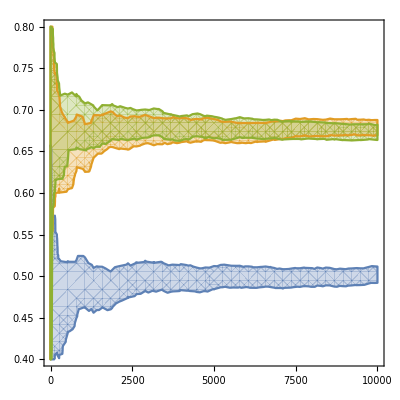

```mathematica
RegionPlot[{IntervalMemberQ[pingFlipIntsPPnaive[[ Ceiling@x ]], y], IntervalMemberQ[pingFlipIntsPPaccurate[[ Ceiling@x ]], y],IntervalMemberQ[pingFlipIntsOurs[[ Ceiling@x ]], y]},{x,1,invLen},{y,0.4,0.8}]
```

```mathematica
(*** TIME-VARIANT SCENARIO ANALYSIS ***)
```

```mathematica
(* loading the files. First index = time step, second index = run *) 
varDataPPnaiveOp= Import[NotebookDirectory[]<>"generated_data/time_variant/time_variant_baseline_var_op_naive.csv"]//Transpose;
varDataPPnaiveTool= Import[NotebookDirectory[]<>"generated_data/time_variant/time_variant_baseline_var_tool_naive.csv"]//Transpose;
varDataPPaccurateOp= Import[NotebookDirectory[]<>"generated_data/time_variant/time_variant_baseline_var_op_accurate.csv"]//Transpose;
varDataPPaccurateTool= Import[NotebookDirectory[]<>"generated_data/time_variant/time_variant_baseline_var_tool_accurate.csv"]//Transpose;
varDataOursOp= Import[NotebookDirectory[]<>"generated_data/time_variant/time_variant_ours_var_op.csv"]//Transpose;
varDataOursTool= Import[NotebookDirectory[]<>"generated_data/time_variant/time_variant_ours_var_tool.csv"]//Transpose;
```

```mathematica
varRunLen = (Dimensions@varDataOursOp)[[1]]; 
varRunCt = (Dimensions@varDataOursOp)[[2]];
```

```mathematica
(* Test 1: marginals of Op over time *)
```

```mathematica
interWilson[Count[varDataPPnaiveOp[[99]],  "ok"],varRunCt, 0.95]
interWilson[Count[varDataPPaccurateOp[[99]], "ok"],varRunCt, 0.95]
interWilson[Count[varDataOursOp[[99]], "ok"],varRunCt, 0.95]
```

Interval[{0.774081,0.823623}]

Interval[{0.752243,0.803622}]

Interval[{0.742913,0.79502}]

```mathematica
interWilson[Count[varDataPPnaiveOp[[50]],  "ok"],varRunCt, 0.95]
interWilson[Count[varDataPPaccurateOp[[50]], "ok"],varRunCt, 0.95]
interWilson[Count[varDataOursOp[[50]], "ok"],varRunCt, 0.95]
```

Interval[{0.798121,0.845407}]

Interval[{0.767831,0.817919}]

Interval[{0.753281,0.804577}]

```mathematica
interWilson[Count[varDataPPnaiveOp[[25]],  "ok"],varRunCt, 0.95]
interWilson[Count[varDataPPaccurateOp[[25]], "ok"],varRunCt, 0.95]
interWilson[Count[varDataOursOp[[25]], "ok"],varRunCt, 0.95]
```

Interval[{0.773039,0.822673}]

Interval[{0.774081,0.823623}]

Interval[{0.784517,0.833111}]

```mathematica
okOpIntNaive = Table[interWilson[Count[varDataPPnaiveOp[[i]],  "ok"],varRunCt, 0.95], {i,1,varRunLen}];
okOpIntAccurate= Table[interWilson[Count[varDataPPaccurateOp[[i]],  "ok"],varRunCt, 0.95], {i,1,varRunLen}];
okOpIntOurs= Table[interWilson[Count[varDataOursOp[[i]],  "ok"],varRunCt, 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

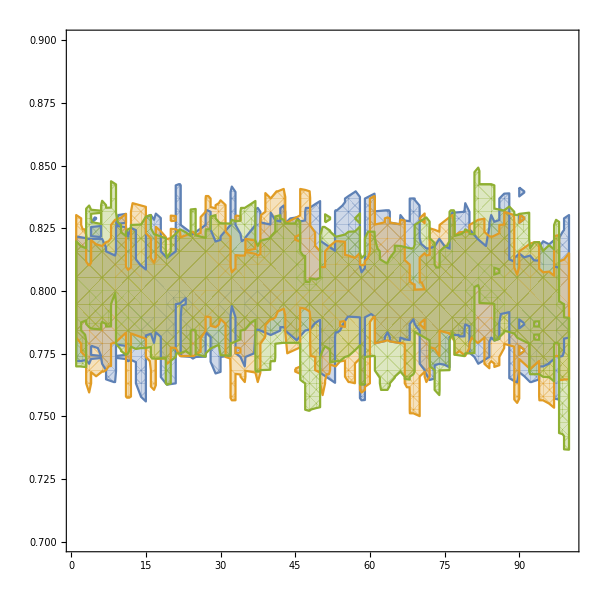

```mathematica
RegionPlot[{IntervalMemberQ[okOpIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[okOpIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[okOpIntOurs[[ Ceiling@x ]], y]},{x,1,varRunLen},{y,0.7,0.9}]
```

```mathematica
(* marginal of tool being functional *) 
okToolIntNaive = Table[interWilson[Count[varDataPPnaiveTool[[i]],  "func"],varRunCt, 0.95], {i,1,varRunLen}];
okToolIntAccurate= Table[interWilson[Count[varDataPPaccurateTool[[i]],  "func"],varRunCt, 0.95], {i,1,varRunLen}];
okToolIntOurs= Table[interWilson[Count[varDataOursTool[[i]],  "func"],varRunCt, 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

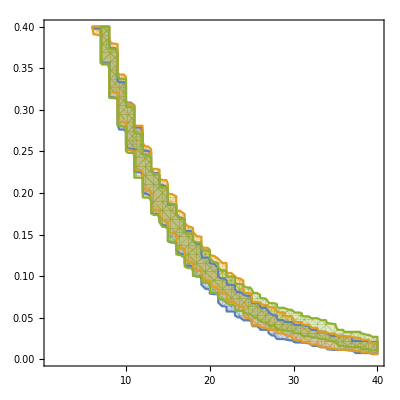

```mathematica
RegionPlot[{IntervalMemberQ[okToolIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[okToolIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[okToolIntOurs[[ Ceiling@x ]], y]},{x,1,40},{y,0.0,0.4}]
```

```mathematica
(* utility functions: return the (tool, op) pair at time step i *) 
toolAndOpNaive[i_]:= Transpose[{varDataPPnaiveTool[[i]], varDataPPnaiveOp[[i]]}];
toolAndOpAccurate[i_]:= Transpose[{varDataPPaccurateTool[[i]], varDataPPaccurateOp[[i]]}];
toolAndOpOurs[i_]:= Transpose[{varDataOursTool[[i]], varDataOursOp[[i]]}];
```

```mathematica
(* joint of op and tool being ok over time *) 
bothOkIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"func","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
bothOkIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"func","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
bothOkIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"func","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

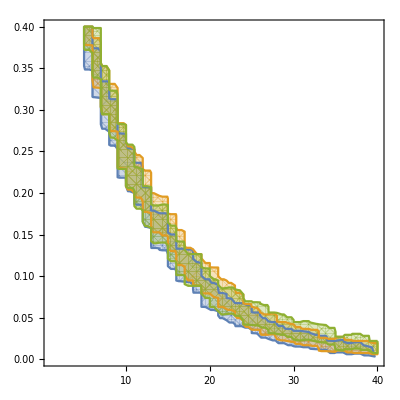

```mathematica
RegionPlot[{IntervalMemberQ[bothOkIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[bothOkIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[bothOkIntOurs[[ Ceiling@x ]], y]},{x,1,40},{y,0,0.4}]
```

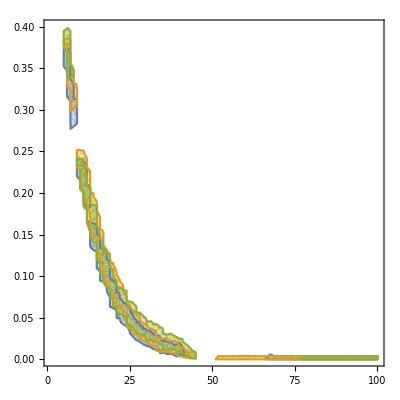

```mathematica
(* joint tool and not op *) 
(* returns the pair at time step i *)
```

```mathematica
toolOkOpNotIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"func","fail"}],varRunCt, 0.95], {i,1,varRunLen}];
toolOkOpNotIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"func","fail"}],varRunCt, 0.95], {i,1,varRunLen}];
toolOkOpNotIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"func","fail"}],varRunCt, 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

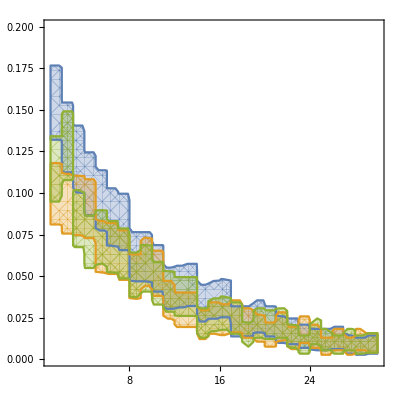

```mathematica
RegionPlot[{IntervalMemberQ[toolOkOpNotIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[toolOkOpNotIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[toolOkOpNotIntOurs[[ Ceiling@x ]], y]},{x,1,30},{y,0,0.2}]
```

```mathematica
(* joint tool not ok, op ok *)
```

```mathematica
toolNotOpOkIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"broken","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
toolNotOpOkIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"broken","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
toolNotOpOkIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"broken","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

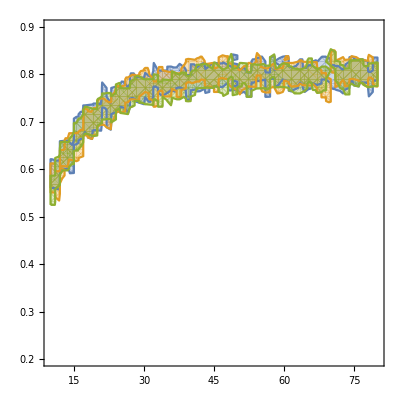

```mathematica
RegionPlot[{IntervalMemberQ[toolNotOpOkIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[toolNotOpOkIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[toolNotOpOkIntOurs[[ Ceiling@x ]], y]},{x,10,80},{y,0.2,0.9}]
```

```mathematica
(* neither ok, ok *)
```

```mathematica
neitherOkIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"broken","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
neitherOkIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"broken","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
neitherOkIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"broken","ok"}],varRunCt, 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

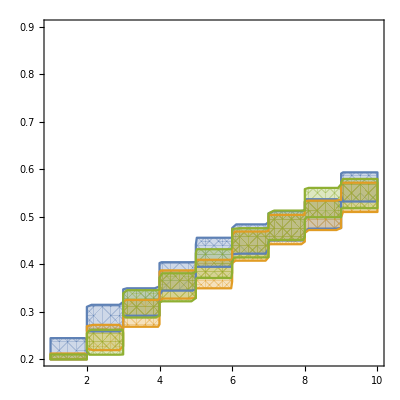

```mathematica
RegionPlot[{IntervalMemberQ[neitherOkIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[neitherOkIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[neitherOkIntOurs[[ Ceiling@x ]], y]},{x,1,10},{y,0.2,0.9}]
```

```mathematica
(* now back to "within timestep" view *)
```

```mathematica
interWilson[Count[varDataPPnaiveOp[[25]],  "ok"],varRunCt, 0.95]
interWilson[Count[varDataPPaccurateOp[[25]], "ok"],varRunCt, 0.95]
interWilson[Count[varDataOursOp[[25]], "ok"],varRunCt, 0.95]
```

Interval[{0.773039,0.822673}]

Interval[{0.774081,0.823623}]

Interval[{0.784517,0.833111}]

```mathematica
interWilson[Count[varDataPPnaiveTool[[25]],  "func"],varRunCt, 0.95]
interWilson[Count[varDataPPaccurateTool[[25]], "func"],varRunCt, 0.95]
interWilson[Count[varDataOursTool[[25]], "func"],varRunCt, 0.95]
```

Interval[{0.0468965,0.0764711}]

Interval[{0.0495497,0.0797949}]

Interval[{0.0548839,0.0864147}]

```mathematica
(* conditional tool = func | op = ok over time *) 
condOkIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"func","ok"}],Count[toolAndOpNaive[i],  {_,"ok"}], 0.95], {i,1,30}];
condOkIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"func","ok"}],Count[toolAndOpAccurate[i],  {_,"ok"}], 0.95], {i,1,30}];
condOkIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"func","ok"}],Count[toolAndOpOurs[i],  {_,"ok"}], 0.95], {i,1,30}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

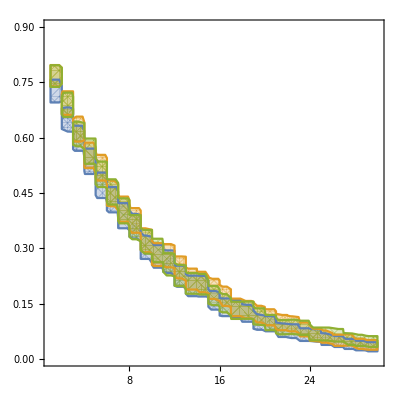

```mathematica
RegionPlot[{IntervalMemberQ[condOkIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[condOkIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[condOkIntOurs[[ Ceiling@x ]], y]},{x,1,30},{y,0,0.9}]
```

```mathematica
(* conditional op = ok | tool = func over time *) 
condotherOkIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"func","ok"}],Count[toolAndOpNaive[i],  {"func",_}], 0.95], {i,1,50}];
condotherOkIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"func","ok"}],Count[toolAndOpAccurate[i],  {"func",_}], 0.95], {i,1,50}];
condotherOkIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"func","ok"}],Count[toolAndOpOurs[i],  {"func",_}], 0.95], {i,1,50}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

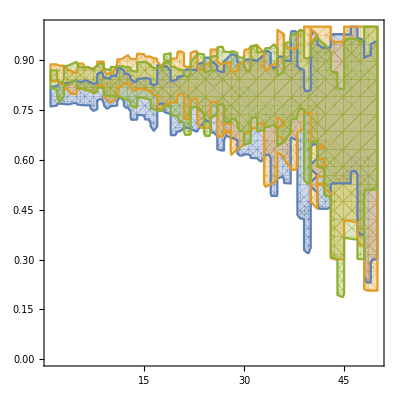

```mathematica
RegionPlot[{IntervalMemberQ[condotherOkIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[condotherOkIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[condotherOkIntOurs[[ Ceiling@x ]], y]},{x,1,50},{y,0,1}]
```

```mathematica
(* conditional op = ok | tool = broken over time *) 
condOkToolBrokeIntNaive = Table[interWilson[Count[toolAndOpNaive[i],  {"broken","ok"}],Count[toolAndOpNaive[i],  {"broken",_}], 0.95], {i,1,varRunLen}];
condOkToolBrokeIntAccurate= Table[interWilson[Count[toolAndOpAccurate[i],  {"broken","ok"}],Count[toolAndOpAccurate[i],  {"broken",_}], 0.95], {i,1,varRunLen}];
condOkToolBrokeIntOurs= Table[interWilson[Count[toolAndOpOurs[i],  {"broken","ok"}],Count[toolAndOpOurs[i],  {"broken",_}], 0.95], {i,1,varRunLen}];
```

Part::pkspec1: The expression Ceiling[x] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

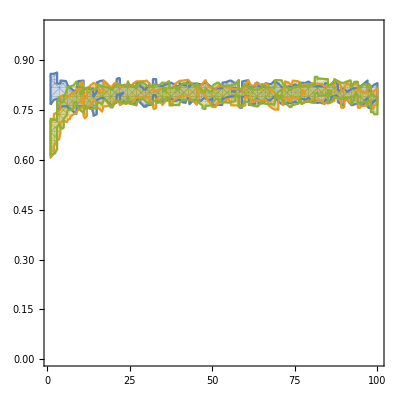

```mathematica
RegionPlot[{IntervalMemberQ[condOkToolBrokeIntNaive[[ Ceiling@x ]], y], IntervalMemberQ[condOkToolBrokeIntAccurate[[ Ceiling@x ]], y],IntervalMemberQ[condOkToolBrokeIntOurs[[ Ceiling@x ]], y]},{x,1,varRunLen},{y,0,1}]
```